```mathematica
ClearAll["Global`*"]
```

```mathematica
Needs["NumericalCalculus`"]
```

### Task & Variables

Analyze waveguide dispersion and total dispersion in a fiber waveguide

```mathematica
a=3×10^-6;
(*λ=1500×10^-9;*)
m=0;
n=0;
c=3×10^8;
(*k0=(2×π)/λ;*)
```

```mathematica
λ[ω_]:=(2×π×c)/ω;
```

Calculating material dispersion according to Selmeier’s formula

```mathematica
as1=0.69616630;
as2=0.40794260;
as3=0.89747940;
ls1=0.0684043×10^-6;
ls2=0.11624140×10^-6;
ls3=9.8961610×10^-6;
nclad[ω_]:=Sqrt[1+(as1×λ[ω]^2)/(λ[ω]^2-(ls1)^2)+(as2×λ[ω]^2)/(λ[ω]^2-(ls2)^2)+(as3×λ[ω]^2)/(λ[ω]^2-(ls3)^2)];
dn=5×10^-3;
ncore[ω_]:=nclad[ω]+dn;
```

### Calculations

```mathematica
k0[ω_]:=(2×π)/λ[ω];
u[neff_,ω_,r_]:=r×k0[ω]×√(ncore[ω]^2-neff^2);
w[neff_,ω_,r_]:=r×k0[ω]×√(neff^2-nclad[ω]^2);
```

```mathematica
NEff[ω_]:=neff/.FindRoot[w[neff,ω,a]BesselJ[m,u[neff,ω,a]]×BesselK[m-1,w[neff,ω,a]]+u[neff,ω,a]BesselJ[m-1,u[neff,ω,a]]×BesselK[m,w[neff,ω,a]]==0,{neff,ncore[ω]-10^-9}]
```

```mathematica
Plot[NEff[ω],{ω,1.1×10^15,1.57×10^15},AxesLabel->{"Frequency [Hz]","n_eff"},ImageSize->Large]
```

-Graphics-

```mathematica
A[ω_]:=BesselJ[m,u[NEff[ω],ω,a]]/BesselK[m,w[NEff[ω],ω,a]];
```

```mathematica
R[ω_,r_]:=Piecewise[{{BesselJ[m,u[NEff[ω],ω,r]],r<a},{A[ω]×BesselK[m,w[NEff[ω],ω,r]],r>a}}];
```

#### Waveguide main mode

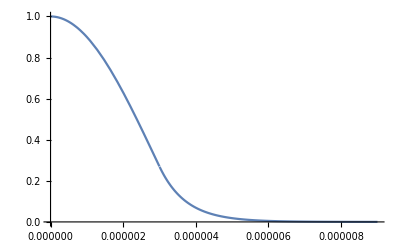

```mathematica
Plot[R[(2×π×c)/(0.550×10^-6),r],{r,0,3×a},PlotRange->All]
```

```mathematica
βtab=Table[{ω,NEff[ω]×k0[ω]},{ω,1.1×10^15,1.885×10^15,10^13}];
βfit[ω_]=Fit[βtab,{1,ω,ω^2,ω^3,ω^4},ω];
β2[ω_]=D[βfit[ω],{ω,2}];
```

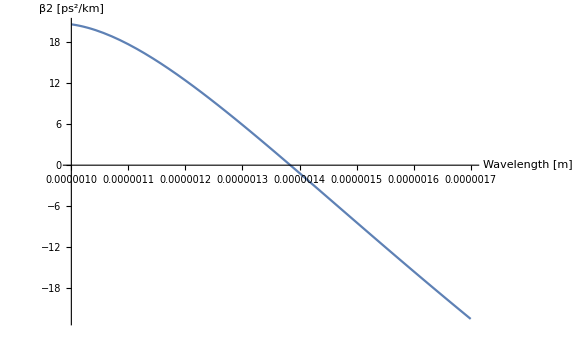

```mathematica
Plot[β2[(2×π×c)/λ]×10^27,{λ,1.0×10^-6,1.7×10^-6},AxesLabel->{"Wavelength [m]","β2 [ps^2/km]"},ImageSize->Large]
```

```mathematica
FindRoot[β2[(2×π×c)/λ],{λ,1.3×10^-6}]
```

{λ→1.38382×10^-6}

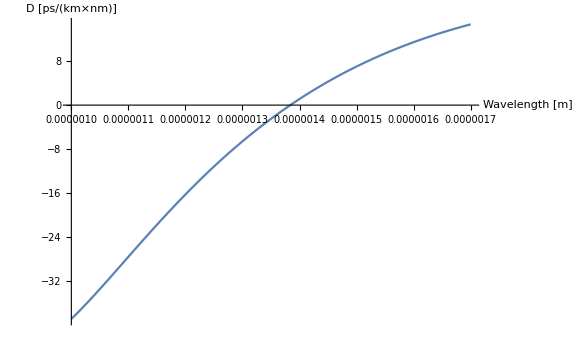

```mathematica
Disp[ω_]=-ω^2/(2×π×c)×β2[ω];
Plot[Disp[(2×π×c)/λ]×10^6,{λ,1.0×10^-6,1.7×10^-6},AxesLabel->{"Wavelength [m]","D [ps/(km×nm)]"},ImageSize->Large]
```

```mathematica
β2=Table[0,{i,Length[βtab]},{j,2}];
For[i=1,i≤Length[β2],i++,β2[[i,1]]=λ[βtab[[i,1]]]];
For[i=3,i<Length[β2]-1,i++,β2[[i,2]]=((-βtab[[i+2,2]]+16βtab[[i+1,2]]-30×βtab[[i,2]]+16βtab[[i-1,2]]-βtab[[i-2,2]])/(12×(βtab[[2,1]]-βtab[[1,1]])^2))×10^27];
```

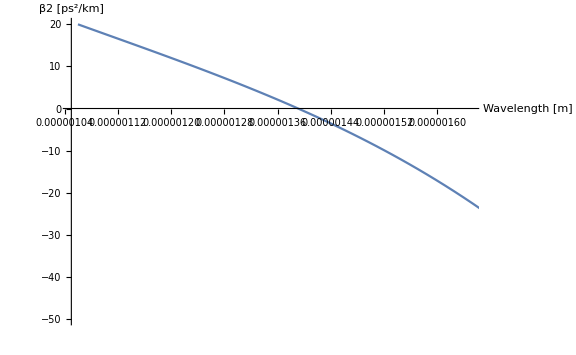

```mathematica
ListLinePlot[β2,PlotRange->{{1.05×10^-6,1.65×10^-6},{-50,20}},AxesLabel->{"Wavelength [m]","β2 [ps^2/km]"},ImageSize->Large]
```

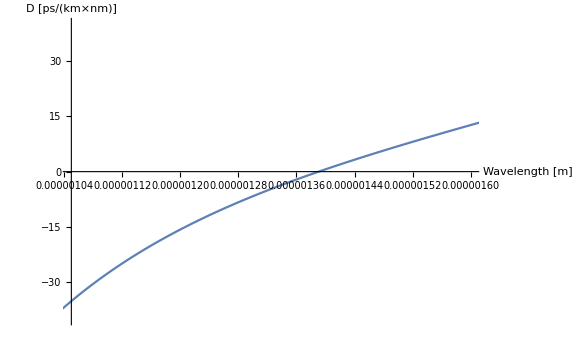

```mathematica
Disp=Table[0,{i,Length[βtab]},{j,2}];
For[i=1,i≤Length[Disp],i++,Disp[[i,1]]=λ[βtab[[i,1]]]];
For[i=3,i<Length[Disp]-1,i++,Disp[[i,2]]=(-2×π×c)/Disp[[i,1]]^2×β2[[i,2]]×10^6/10^27];
ListLinePlot[Disp,PlotRange->{{1.05×10^-6,1.6×10^-6},{-40,40}},AxesLabel->{"Wavelength [m]","D [ps/(km×nm)]"},ImageSize->Large]
```

Material dispersion

```mathematica
βmat=Table[{ω,nclad[ω]×k0[ω]},{ω,1.1×10^15,1.885×10^15,10^13}];
β2mat=Table[0,{i,Length[βmat]},{j,2}];
For[i=1,i≤Length[β2mat],i++,β2mat[[i,1]]=λ[βmat[[i,1]]]];
For[i=3,i<Length[β2mat]-1,i++,β2mat[[i,2]]=((-βmat[[i+2,2]]+16βmat[[i+1,2]]-30×βmat[[i,2]]+16βmat[[i-1,2]]-βmat[[i-2,2]])/(12×(βmat[[2,1]]-βmat[[1,1]])^2))×10^27];
```

```mathematica
DispMat=Table[0,{i,Length[βmat]},{j,2}];
For[i=1,i≤Length[DispMat],i++,DispMat[[i,1]]=λ[βmat[[i,1]]]];
For[i=3,i<Length[DispMat]-1,i++,DispMat[[i,2]]=(-2×π×c)/DispMat[[i,1]]^2×β2mat[[i,2]]×10^6/10^27];
```

```mathematica
λ[1.25×10^15]
```

1.50796×10^-6

#### Checking that waveguide dispersion and matrial dispersion result in calculated total dispersion

Waveguide dispersion

```mathematica
uNoMat[neff_,ω_,r_]:=r×k0[ω]×√(ncore[1.25×10^15]^2-neff^2);
wNoMat[neff_,ω_,r_]:=r×k0[ω]×√(neff^2-nclad[1.25×10^15]^2);
NEffNoMat[ω_]:=neff/.FindRoot[wNoMat[neff,ω,a]BesselJ[m,uNoMat[neff,ω,a]]×BesselK[m-1,wNoMat[neff,ω,a]]+uNoMat[neff,ω,a]BesselJ[m-1,uNoMat[neff,ω,a]]×BesselK[m,wNoMat[neff,ω,a]]==0,{neff,ncore[1.25×10^15]-10^-9}]
```

```mathematica
βtabWg=Table[{ω,NEffNoMat[ω]×k0[ω]},{ω,1.1×10^15,1.885×10^15,10^13}];
β2Wg=Table[0,{i,Length[βtabWg]},{j,2}];
For[i=1,i≤Length[β2Wg],i++,β2Wg[[i,1]]=λ[βtabWg[[i,1]]]];
For[i=3,i<Length[β2Wg]-1,i++,β2Wg[[i,2]]=((-βtabWg[[i+2,2]]+16βtabWg[[i+1,2]]-30×βtabWg[[i,2]]+16βtabWg[[i-1,2]]-βtabWg[[i-2,2]])/(12×(βtabWg[[2,1]]-βtabWg[[1,1]])^2))×10^27];
```

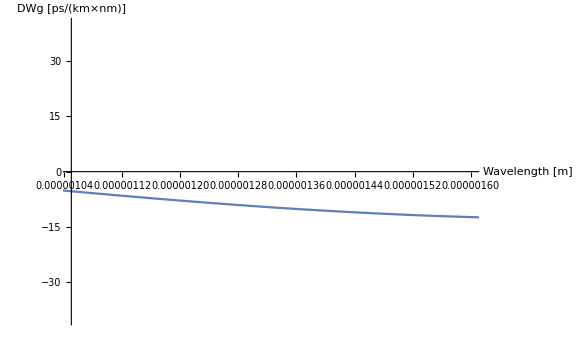

```mathematica
DispWg=Table[0,{i,Length[βtabWg]},{j,2}];
For[i=1,i≤Length[DispWg],i++,DispWg[[i,1]]=λ[βtabWg[[i,1]]]];
For[i=3,i<Length[DispWg]-1,i++,DispWg[[i,2]]=(-2×π×c)/DispWg[[i,1]]^2×β2Wg[[i,2]]×10^6/10^27];
ListLinePlot[DispWg,PlotRange->{{1.05×10^-6,1.6×10^-6},{-40,40}},AxesLabel->{"Wavelength [m]","DWg [ps/(km×nm)]"},ImageSize->Large]
```

Total dispersion

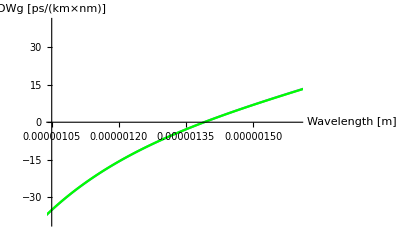

```mathematica
DispTotal=Table[0,{i,Length[βtabWg]},{j,2}];
For[i=1,i≤Length[DispTotal],i++,DispTotal[[i,1]]=DispWg[[i,1]]];
For[i=3,i<Length[DispTotal]-1,i++,DispTotal[[i,2]]=DispWg[[i,2]]+DispMat[[i,2]]];
Show[ListLinePlot[DispTotal,PlotRange->{{1.05×10^-6,1.6×10^-6},{-40,40}},AxesLabel->{"Wavelength [m]","DWg [ps/(km×nm)]"},ImageSize->Full],ListLinePlot[Disp,PlotRange->{{1.05×10^-6,1.6×10^-6},{-40,40}},AxesLabel->{"Wavelength [m]","D [ps/(km×nm)]"},ImageSize->Full,PlotStyle->Green]]
```

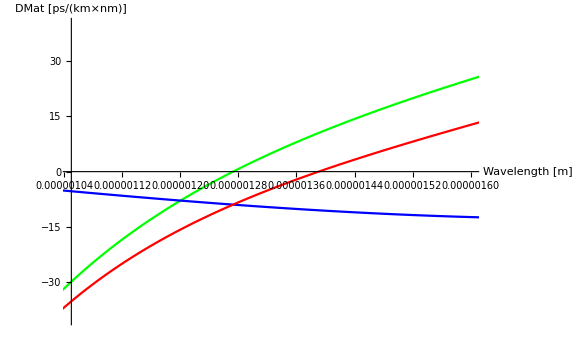

```mathematica
Show[ListLinePlot[DispMat,PlotRange->{{1.05×10^-6,1.6×10^-6},{-40,40}},AxesLabel->{"Wavelength [m]","DMat [ps/(km×nm)]"},ImageSize->Large,PlotStyle->Green],ListLinePlot[DispWg,PlotRange->{{1.05×10^-6,1.6×10^-6},{-40,40}},AxesLabel->{"Wavelength [m]","D [ps/(km×nm)]"},ImageSize->Large,PlotStyle->Blue],ListLinePlot[DispTotal,PlotRange->{{1.05×10^-6,1.6×10^-6},{-40,40}},AxesLabel->{"Wavelength [m]","D [ps/(km×nm)]"},ImageSize->Large,PlotStyle->Red]]
```